# Cleaning Up Yorkeys Knob Dataset

## Functions

```mathematica
Themes`AddThemeRules["GridPoints"
,AspectRatio->1
,DefaultPlotStyle->Thread@Directive[{Purple,Blue,Red},PointSize[.005],Opacity[.4]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,GridLines->Automatic
,GridLinesStyle->Directive[Opacity[.5],LightGray]
]
```

GridPoints

## Data

```mathematica
SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/ThresholdDependent/GeoCleaner"];
```

Yorkeys

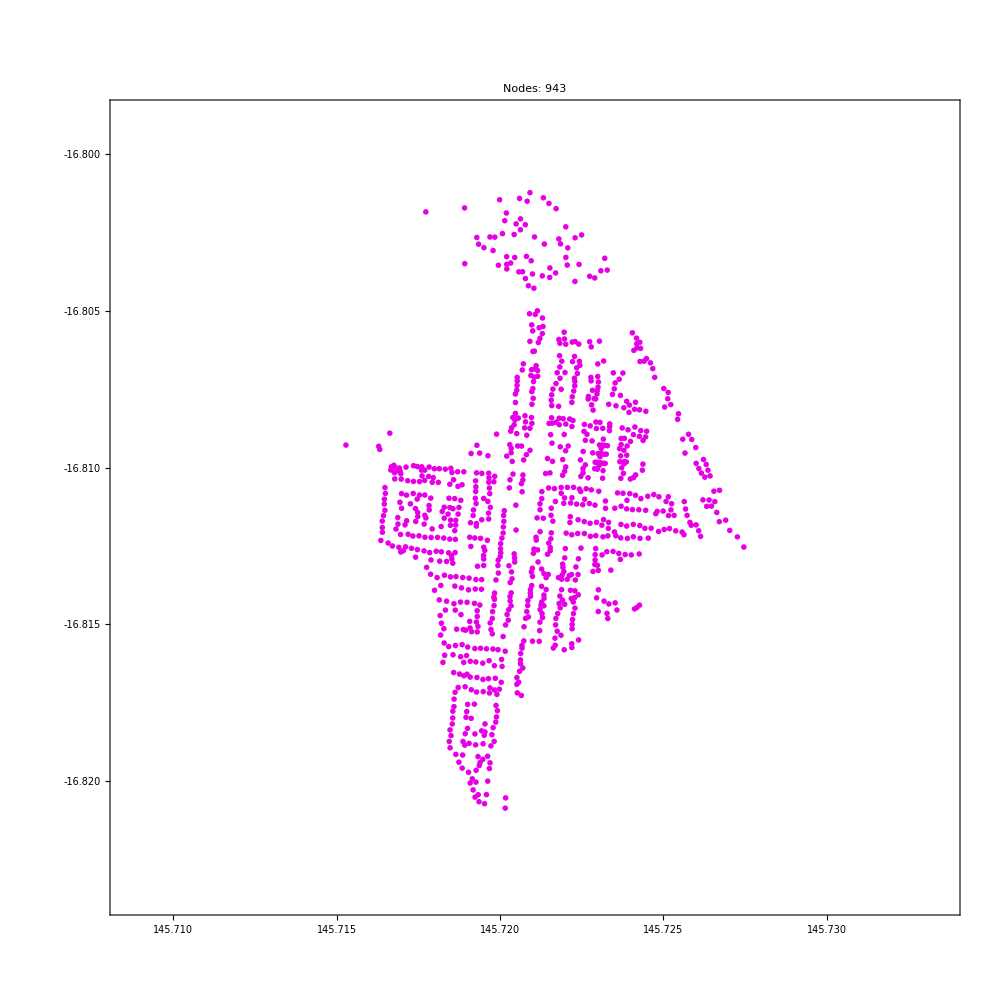

```mathematica
{folder,locationTag}={"./GeoLocations","YorkeysKnob_02"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"];
clustered=FindClusters[rawData//Sort,2];
ListPlot[clustered[[2]]
,AspectRatio->1
,GridLines->None
,ImageSize->1000
,PlotLabel->("Nodes: "<>ToString[Length[rawData]])
,PlotRange->({#-.0125,#+.0125}&/@(Mean/@Transpose[clustered[[2]]]))
,PlotStyle->Directive[{Darker[Magenta,.1],PointSize[.1]}]
,PlotTheme->"Business"
]
(*Export[folder<>"/Curated/images/"<>locationTag<>".jpg",%,ImageResolution->500]*)
(*Export[folder<>"/Curated/"<>locationTag<>".csv",clustered[[2]]]*)
```

Yorkeys and Trinity

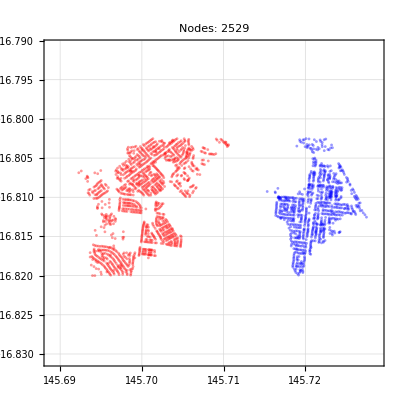

./GeoLocations/Curated/images/YorkeysKnob_01.jpg

./GeoLocations/Curated/YorkeysKnob_01.csv

```mathematica
{folder,locationTag}={"./GeoLocations","YorkeysKnob_01"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"][[2;;All]];
filteredData=Cases[rawData//Sort,{a_,b_}/;(a>145.775||-16.82<b<-16.8025)];
clusteredData=FindClusters[filteredData,2];
ListPlot[clusteredData
,PlotLabel->("Nodes: "<>ToString[Length[rawData]])
,PlotStyle->{Red,Blue}
,PlotTheme->"GridPoints"
,PlotRange->({#-.02,#+.02}&/@(Mean/@Transpose[filteredData]))
]
Export[folder<>"/Curated/images/"<>locationTag<>".jpg",%,ImageResolution->500]
(*Export[folder<>"/Curated/"<>locationTag<>".csv",clusteredData//Flatten[#,1]&]*)
```

Trinity

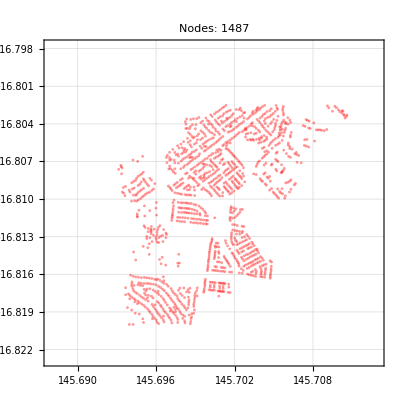

./GeoLocations/Curated/images/YorkeysKnob_03.jpg

./GeoLocations/Curated/YorkeysKnob_03.csv

```mathematica
{folder,locationTag}={"./GeoLocations","YorkeysKnob_03"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"][[2;;All]];
filteredData=Cases[rawData//Sort,{a_,b_}/;(a>145.775||-16.82<b<-16.8025)];
ListPlot[filteredData
,PlotLabel->("Nodes: "<>ToString[Length[rawData]])
,PlotStyle->Red
,PlotTheme->"GridPoints"
,PlotRange->({#-.0125,#+.0125}&/@(Mean/@Transpose[filteredData]))
]
Export[folder<>"/Curated/images/"<>locationTag<>".jpg",%,ImageResolution->500]
(*Export[folder<>"/Curated/"<>locationTag<>".csv",filteredData]*)
```

Gordonvale

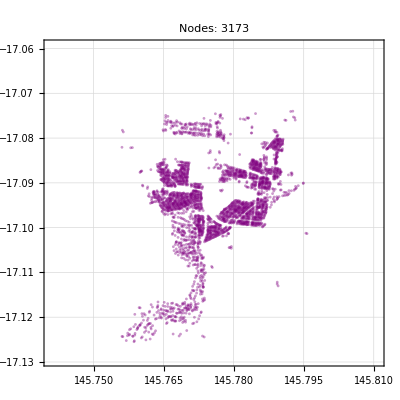

./GeoLocations/Curated/images/Gordonvale_01.jpg

./GeoLocations/Curated/Gordonvale_01.csv

```mathematica
{folder,locationTag}={"./GeoLocations","Gordonvale_01"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"][[2;;All]];
filteredData=rawData//Sort;
ListPlot[filteredData
,PlotLabel->("Nodes: "<>ToString[Length[rawData]])
,PlotTheme->"GridPoints"
,PlotRange->({#-.035,#+.035}&/@(Mean/@Transpose[filteredData]))
]
Export[folder<>"/Curated/images/"<>locationTag<>".jpg",%,ImageResolution->500]
(*Export[folder<>"/Curated/"<>locationTag<>".csv",filteredData]*)
```